```mathematica
Clear["Global`*"]
```

```mathematica
t[f_[x_], n_,x0_:0]:=∑_(i=0)^n (1/(i!)D[f[x],{x,i}]/.{x->x0})x^i
```

```mathematica
t[Sin[x],1]
```

x

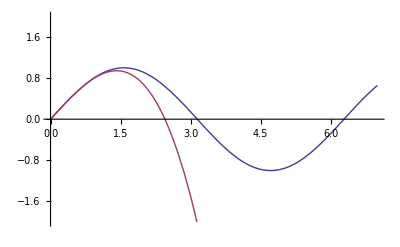

```mathematica
Plot[Evaluate[{Sin[x],t[Sin[x],3]}],{x,0,7},PlotRange -> {-2,2}]
```

```mathematica
g[x_,m_]:=t[Sin[x],m]
```

```mathematica
g[x,5]
```

x-x^3/6+x^5/120

```mathematica
Module[
{f,g},
f[x_]:=Sin[x];
g[x_,n_]:=t[Sin[Mod[x,2 π]],n];
Manipulate[
GraphicsGrid[
{
{
Plot[
Evaluate[{f[x],g[x,n]}],{x,0,70},
PlotRange -> {-2,2},
Epilog->Inset[Text[Style[n,20]],ImageScaled[{0.9,0.1}]]
]
},
{
Plot[Evaluate[Abs[f[x]-g[x,n]]],{x,0,70}]
}
}
],
{n,1,50,1}
]
]
```

```mathematica
Manipulate[Plot[Evaluate[{ⅇ^x,t[ⅇ^x,n]}],{x,0,4},PlotRange -> {0,30}],{n,1,100}]
```

```mathematica
t[ⅇ^x,x,n]
```

t[ⅇ^x,x,n]

```mathematica
(* Dec 29 2009 - let's try to make even more use of the symmetry *)
Module[
{f,g},
f[x_]:=Sin[x];
g[x_,n_]:=t[Sin[x],n] /; 0≤ x < π/2;
g[x_,n_]:=g[π-x,n] /; π/2≤ x < π;
g[x_,n_]:=-g[x-π,n]/; π ≤ x < (3π)/2;
g[x_,n_]:=-g[x-π,n]/; (3π)/2 ≤ x < 2π;
g[x_,n_]:= g[Mod[x,2π],n] /; x ≥ 2π;
Manipulate[
GraphicsGrid[
{
{
Plot[
Evaluate[{f[x],g[x,n]}],{x,0,70},
PlotRange -> {-2,2},
Epilog->Inset[Text[Style[n,20]],ImageScaled[{0.9,0.1}]]
]
},
{
Plot[Evaluate[Abs[f[x]-g[x,n]]],{x,0,70}]
}
}
],
{n,1,50,1}
]
]
```

```mathematica
conditional
```